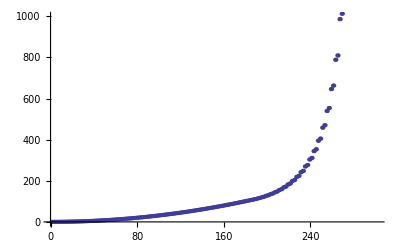

```mathematica
ListPlot[Sort[Re[esys[[1]]]]]
```

```mathematica
ListPlot[Re[esys[[1]][[Ordering[Re[esys[[1]]]]]]]]
```

```mathematica
ListLinePlot[esys[[2]][[Ordering[Re[esys[[1]]]]]][[1]]]
```

```mathematica
(*esys2=esys[[2]][[Ordering[Re[esys[[1]]]]]];*)
esys2=test[[2]][[Ordering[Re[test[[1]]]]]];
Manipulate[
Module[{},
NormEig=Table[{x,Norm[esys2[[n]][x]]^2},{x,0,π,π/200.}];
ReEig=Table[{x,Re[esys2[[n]][x]]},{x,0,π,π/200.}];
ImEig=Table[{x,Im[esys2[[n]][x]]},{x,0,π,π/200.}];
Row[ListLinePlot[{1,ReEig,ImEig},PlotRange-> All,
PlotStyle-> {{Thick,Blue},{Thick,Red},{Thick,Dashed, Red}},
Axes-> True,
Frame-> True,
FrameStyle->Thick,
FrameTicksStyle->Directive[18,Bold],
ImageSize-> 500
],Re[Sort[test[[1]]][[n]]]]
],{n,1,Length[test[[2]]],1}]
(*TODO: one out of every pair of n, n+1 gets an imaginary part of 0 here, but a nonzero imaginary part on plotspectrum - maybe inspect the table individually?*)
```

Part::partd: Part specification esys2 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification test is neither a machine-sized integer nor a list of machine-sized integers.

Part::partw: Part 3 of 1 ⟦ test ⟧ does not exist.

Part::partd: Part specification esys2 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pspec: Part specification test is neither a machine-sized integer nor a list of machine-sized integers.

Part::partw: Part 3 of 1 ⟦ test ⟧ does not exist.

Part::partd: Part specification esys2 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
esys2=esys[[2]][[Ordering[Re[esys[[1]]]]]]
```

```mathematica
Ordering[Re[esys[[1]]]]
```

{21,86,131,199,5,73,188,201,4,193,196,7,8,10,14,181,53,12,195,1,202,198,3,2,6,176,11,194,200,197,13,9,62,63,150,149,56,57,148,153,52,64,147,154,47,61,152,163,33,49,160,183,20,36,185,186,23,18,191,179,31,17,187,170,37,27,171,166,38,30,180,164,41,24,182,161,46,26,172,156,45,32,174,162,39,22,190,169,29,15,192,175,16,28,173,189,25,35,167,168,43,42,155,158,50,60,133,151,54,146,40,58,165,178,55,140,34,51,159,177,19,44,157,184,48,65,126,143,77,68,109,120,89,112,124,104,97,79,137,123,80,71,118,110,107,93,106,101,127,121,91,108,90,136,145,138,59,69,134,144,66,78,141,139,70,82,129,142,67,76,135,130,84,72,113,114,94,85,100,96,81,99,75,111,102,83,88,92,116,122,95,128,115,87,125,117,98,74,132,105,103,119}

```mathematica
Clear[n]
n=101;
Sum[(n-(-1)^(x+n) n)/(x^2-n^2),{x,n+1,Infinity}]+Sum[(n-(-1)^(x+n) n)/(x^2-n^2),{x,0,n-1}]
```

-1/101